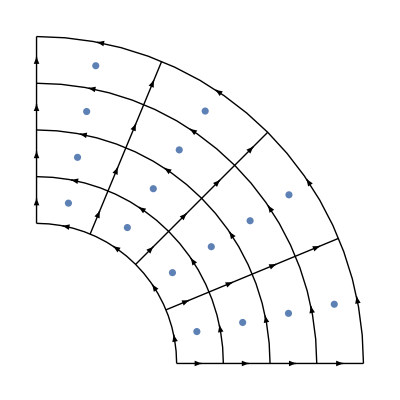

```mathematica
sk[r_] := Graphics[Circle[{0,0},r,{0,Pi/2}]]
Rmax=7; Rmin=3; dang = Pi/8; dmax = Pi/2; dr = 1; d=0.01;
ra[ang_]:=Graphics[Line[{{Rmin Cos[ang],Rmin Sin[ang]},{Rmax Cos[ang],Rmax Sin[ang]}}]]
do[ang_]:=Graphics[ListPlot[Table[{r Cos[ang],r Sin[ang]},{r,Rmin+dr/2,Rmax,dr}]]]
rarr[ang_]:=Graphics[{Arrowheads[0.015],Table[Arrow[{{r Cos[ang],r Sin[ang]},(1+d){r Cos[ang],r Sin[ang]}}],{r,Rmin+dr/2,Rmax,dr}]}]
farr[ang_]:=Graphics[{Arrowheads[0.015],Table[Arrow[{{r Cos[ang],r Sin[ang]},{r Cos[ang],r Sin[ang]}+d{-r Sin[ang],r Cos[ang]}}],{r,Rmin,Rmax,dr}]}]
Show[
Table[sk[p],{p,Rmin,Rmax,dr}],
Table[ra[a],{a,0,dmax,dang}],
Table[do[a],{a,dang/2,dmax,dang}],
Table[rarr[a],{a,0,dmax,dang}],
Table[farr[a],{a,dang/2,dmax,dang}],
ImageSize->Full]
```